# Supplementary Information

SI for the master thesis of ISHII Hidemasa (AY 2022).

```mathematica
(*Figures will be exported to the same directory as this nb file*)
SetDirectory[NotebookDirectory[]];
```

## 1. Introduction

```mathematica
Clear["Global`*"]
```

#### Figure 1.2

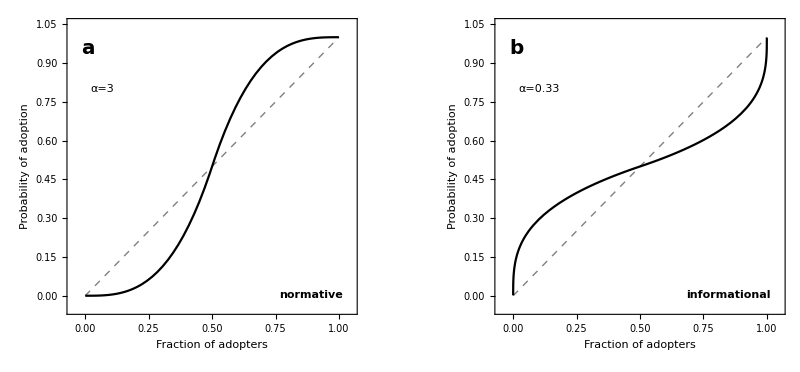

```mathematica
(*Examples for conformity function*)
fconf[x_]:=If[x≤1/2,(2x)^α/2,1-(2(1-x))^α/2];
plots=Table[Plot[{
Style[x,Thick,Dashed,Gray],
Style[fconf[x]/.{α->param[[1]]},Black]},
{x,0,1},
Frame->True,FrameLabel->{
Style["Fraction of adopters",Black,FontSize->12],
Style["Probability of adoption",Black,FontSize->12]
},PlotRange->{{-0.05,1.05},{-0.05,1.05}},
AspectRatio->1,ImageSize->200,
Epilog->{
Text[Style[param[[2]],Bold,FontSize->20],Scaled[{0.05,0.9}],{-1,0}],
Text[StringForm["α=`1`",param[[1]]], Scaled[{0.08,0.78}],{-1,1}],
Text[Style[param[[3]],Bold,Medium], Scaled[{0.95,0.05}],{1,-1}]
}
],{param,{{3,"a","normative"},{0.33,"b","informational"}}}
];
fig=GraphicsRow[plots,Spacings->30]
Export["conformity-bias.pdf",fig];
```

## 2. Threshold model for university enrolment

```mathematica
Clear["Global`*"]
```

## Model formulation

```mathematica
$Assumptions={0≤x≤1,0≤p≤1,0≤θ≤1,γ>0,β>0,0≤ρ≤1};
```

```mathematica
(*Effect of social origins*)
go[x_,θ_]:=1/(1+Exp[-γ(x-θ)]);
goinv[y_,θ_]:=θ+1/γ *Log[y/(1-y)];
fo[x_,θ_]:=(go[x,θ]-go[0,θ])/(go[1,θ]-go[0,θ])-1/2;
foinv[y_,θ_]:=goinv[go[0,θ]+(go[1,θ]-go[0,θ])*(y+1/2),θ];
```

```mathematica
(*Effect of peers*)
gi[q_]:=1/(1+Exp[β(q-1/2)]);
fi[q_]:=(gi[q]-gi[1])/(1-2gi[1])-1/2;
```

```mathematica
(*Dynamics of enrolment rate*)
f[p_]:=1-foinv[-ρ*fi[1-p],θ];
```

## Equations in thesis

```mathematica
(*f(p)*)
Simplify[f[p]]//TraditionalForm
```

-θ-(log((1/(ⅇ^(γ θ)+1)+1/2 (1/(ⅇ^(γ (θ-1))+1)-1/(ⅇ^(γ θ)+1)) (-(2 ⅇ^(β/2) ρ (ⅇ^(β p)-1))/((ⅇ^(β/2)-1) (ⅇ^(β/2)+ⅇ^(β p)))+ρ+1))/(-1/(ⅇ^(γ θ)+1)-1/2 (1/(ⅇ^(γ (θ-1))+1)-1/(ⅇ^(γ θ)+1)) (-(2 ⅇ^(β/2) ρ (ⅇ^(β p)-1))/((ⅇ^(β/2)-1) (ⅇ^(β/2)+ⅇ^(β p)))+ρ+1)+1)))/γ+1

```mathematica
(*Derivative f'(p)*)
FullSimplify[D[f[p],p]]//TraditionalForm
```

(4 (ⅇ^β-1) β (ⅇ^γ-1) ρ (ⅇ^(γ θ)+1) (ⅇ^(γ θ)+ⅇ^γ) ⅇ^(β (p+1/2)))/(γ (-2 ⅇ^(β/2+γ θ)+2 ⅇ^(β+γ θ)-(ρ-1) ⅇ^(β+γ)-(ρ+1) ⅇ^(β/2+γ)+ⅇ^(β/2) (ρ-1)+ⅇ^β (ρ+1)-2 ⅇ^(γ θ+β p)+2 ⅇ^(γ θ+β (p+1/2))+(ρ-1) ⅇ^(γ+β p)+(ρ+1) ⅇ^(γ+β (p+1/2))-(ρ-1) ⅇ^(β (p+1/2))-(ρ+1) ⅇ^(β p)) (ⅇ^(γ θ) ((ρ-1) ⅇ^(β/2+γ)+(ρ+1) ⅇ^(β+γ)-ⅇ^β (ρ-1)-ⅇ^(β/2) (ρ+1)-(ρ-1) ⅇ^(γ+β (p+1/2))-(ρ+1) ⅇ^(γ+β p)+(ρ-1) ⅇ^(β p)+(ρ+1) ⅇ^(β (p+1/2)))+2 (ⅇ^(β/2)-1) ⅇ^γ (ⅇ^(β/2)+ⅇ^(β p))))

```mathematica
(*if γ=β, ρ=1, and θ=1/2 hold, then f(p)=p*)
Simplify[f[p]/.{γ->β,ρ->1,θ->1/2}]//TraditionalForm
```

p

```mathematica
(*f(0)*)
Simplify[f[0]]//TraditionalForm
```

-(log((2 ⅇ^(γ-γ θ)+ⅇ^γ (ρ+1)-ρ+1)/(2 ⅇ^(γ θ)-ⅇ^γ (ρ-1)+ρ+1)))/γ-θ+1

```mathematica
(*f(1)*)
Simplify[f[1]]//TraditionalForm
```

-(log((2 ⅇ^(γ-γ θ)-ⅇ^γ (ρ-1)+ρ+1)/(2 ⅇ^(γ θ)+ⅇ^γ (ρ+1)-ρ+1)))/γ-θ+1

```mathematica
(*f(p) with θ=1/2*)
Simplify[f[p]/.θ->1/2]//TraditionalForm
```

1/2-(log(((ⅇ^(γ/2)-1) (-(2 ⅇ^(β/2) ρ (ⅇ^(β p)-1))/((ⅇ^(β/2)-1) (ⅇ^(β/2)+ⅇ^(β p)))+ρ+1)+2)/(2 (ⅇ^(γ/2)+1) (-1/(ⅇ^(γ/2)+1)-((ⅇ^(γ/2)-1) (-(2 ⅇ^(β/2) ρ (ⅇ^(β p)-1))/((ⅇ^(β/2)-1) (ⅇ^(β/2)+ⅇ^(β p)))+ρ+1))/(2 (ⅇ^(γ/2)+1))+1))))/γ

## Figures in thesis

#### Figure 2.1

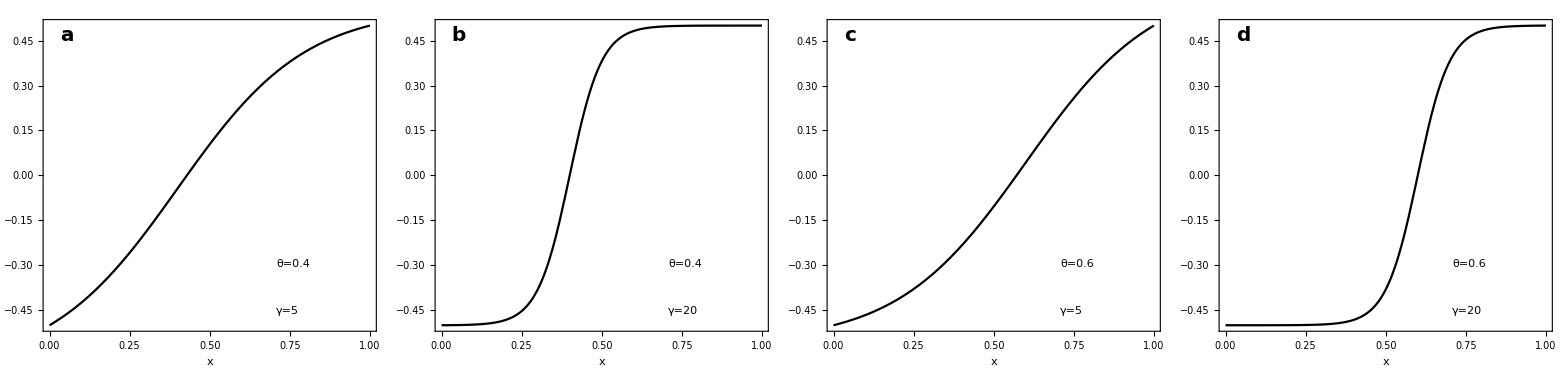

```mathematica
(*Plot f_{org} with several parameter values*)
plots=Table[Plot[
Style[fo[x,θ]/.{θ->param[[1]],γ->param[[2]]},Black],
{x,0,1},
Frame->True,FrameLabel->{"x",None},PlotRange->{{0,1},{-1/2,1/2}},
AspectRatio->1,ImageSize->Medium,
Epilog->{
Text[Style[param[[3]],Bold,FontSize->20],Scaled[{0.05,0.98}],{-1,1}],
Text[StringForm["θ=`1`",param[[1]]], Scaled[{0.7,0.2}],{-1,-1}],
Text[StringForm["γ=`1`",param[[2]]], Scaled[{0.7,0.05}],{-1,-1}]
}
],{param,{{0.4,5,"a"},{0.4,20,"b"},{0.6,5,"c"},{0.6,20,"d"}}}
];
fig=GraphicsRow[plots,Spacings->0]
Export["forg.pdf",fig];
```

#### Figure 2.3

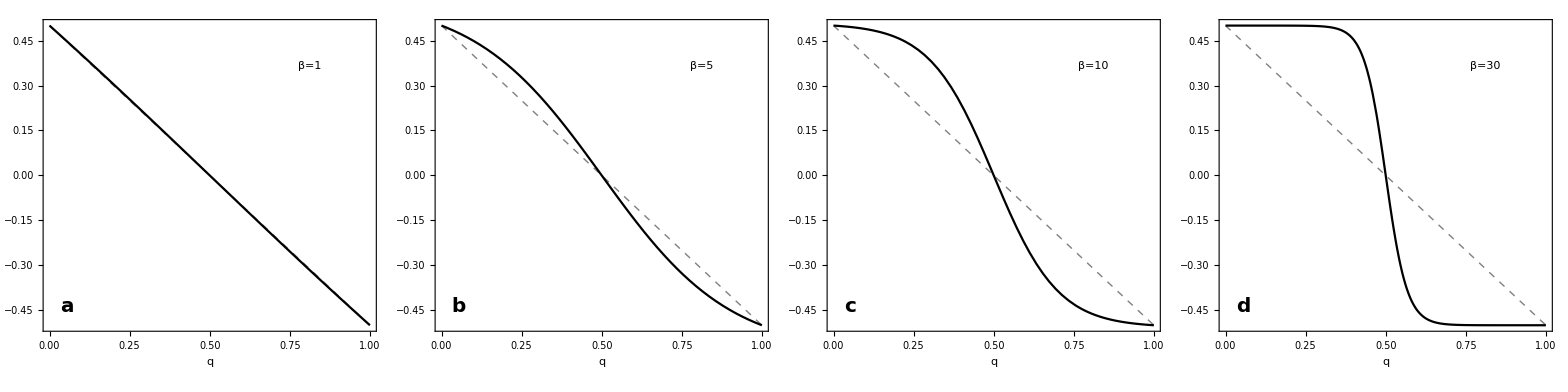

```mathematica
(*Plot f_{int} with several β values*)
plots=Table[Plot[{
Style[-q+1/2,Gray,Dashed,Thick],
Style[fi[q]/.{β->param[[2]]},Black]
},
{q,0,1},
Frame->True,FrameLabel->{"q",None},PlotRange->{{0,1},{-1/2,1/2}},
AspectRatio->1,ImageSize->Medium,
Epilog->{
Text[Style[param[[1]],Bold,FontSize->20],Scaled[{0.05,0.05}],{-1,-1}],
Text[StringForm["β=`1`",param[[2]]], Scaled[{0.8,0.85}]]
}
],{param,{{"a",1},{"b",5},{"c",10},{"d",30}}}
];
fig=GraphicsRow[plots,Spacings->0]
Export["fint.pdf",fig];
```

#### Figure 2.2

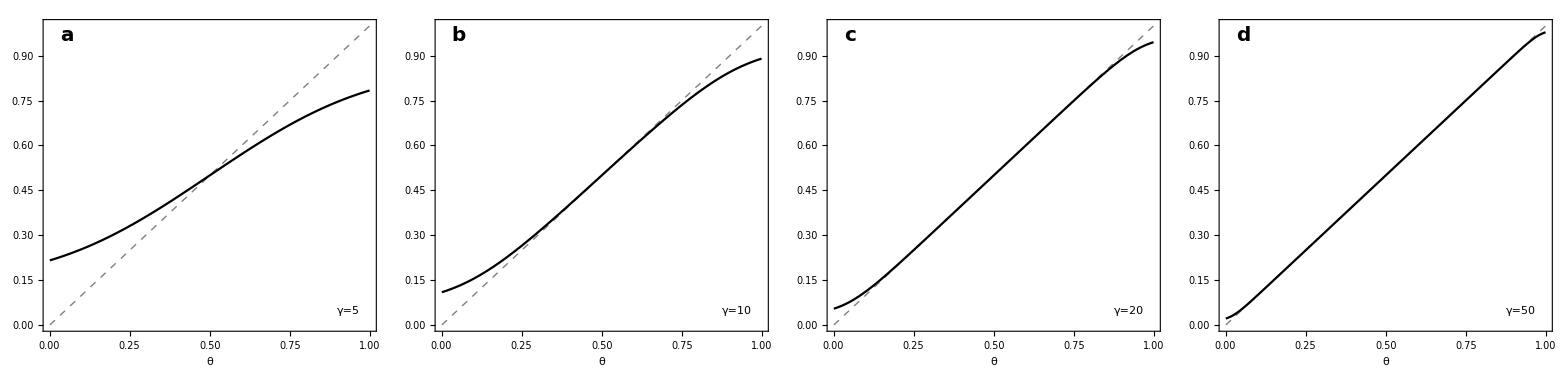

```mathematica
(*The fraction of pupils from disadvantaged families (without university degree)*)
m[θ_]:=(go[0,θ]+go[1,θ])/2;
plots=Table[Plot[{
Style[θ,Gray,Dashed,Thick],
Style[θ+1/γ*Log[m[θ]/(1-m[θ])]/.γ->param[[2]],Black]
},{θ,0.001,0.999},
Frame->True,FrameLabel->{"θ",None},PlotRange->{{0,1},{0,1}},
AspectRatio->1,ImageSize->Small,
Epilog->{
Text[Style[param[[1]],Bold,FontSize->20],Scaled[{0.05,0.98}],{-1,1}],
Text[StringForm["γ=`1`",param[[2]]], Scaled[{0.95,0.05}],{1,-1}]
}],{param,{{"a",5},{"b",10},{"c",20},{"d",50}}}
];
fig=GraphicsRow[plots,Spacings->0]
Export["lowerclass-theta.pdf",fig];
```

## 4. Diffusion of university enrolment

```mathematica
Clear["Global`*"];
```

## Figures in thesis

```mathematica
f[x_,r_]:=-x(x-r)(x-1);(*Schloegl model*)
potf[x_,r_]:=x^4/4-(1+r)/3*x^3+r/2*x^2;(*Potential*)
dotf[x_,r_]:=D[potf[v,r],{v,2}]/.v->x;(*Derivative*)
```

### Plot reaction term and its potential

#### Figure 4.1

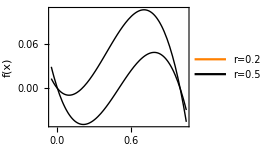

```mathematica
With[{r1=0.2,r2=0.5},
fig=Plot[
{Style[f[x,r1],Orange],Style[f[x,r2],Black]},{x,-0.05,1.05},
Frame->True,AspectRatio->Full,
FrameLabel->{Style["x",Black,FontSize->12],Style["f(x)",Black,FontSize->12]},
PlotLegends->{StringForm["r=`1`",r1],StringForm["r=`1`",r2]},
ImageSize->{200,150}
]
]
Export["schloegl.pdf",fig];
```

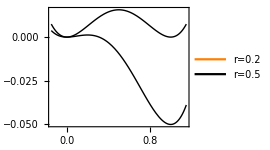

```mathematica
With[{r1=0.2,r2=0.5},
fig=Plot[
{Style[potf[x,r1],Orange],Style[potf[x,r2],Black]},{x,-0.15,1.15},
Frame->True,AspectRatio->Full,
FrameLabel->{Style["x",Black,FontSize->12],Style["F(x)",Black,FontSize->12]},
PlotLegends->{StringForm["r=`1`",r1],StringForm["r=`1`",r2]},
ImageSize->{200,150}
]
]
Export["schloegl_pot.pdf",fig];
```

### Mean escape time in the case of N = 1

#### Figure 4.2

```mathematica
(*Mean escape time from quiescent state to neighbourhood of active state*)
esctime[r_]:=2π/Sqrt[dotf[0,r]*(-dotf[r,r])]*Exp[(potf[r,r]-potf[0,r])/(α^2/2)];
```

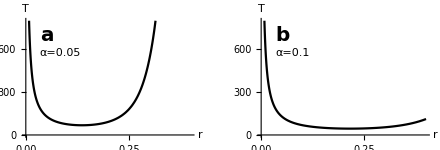

```mathematica
plots=Table[Plot[
Style[esctime[r]/.α->param[[1]],Black],{r,0.005,0.4},
ImageSize->{200,150},PlotRange->{{0,0.4},{0,800}},
AxesLabel->{Style["r",Black,FontSize->12],Style["T",Black,FontSize->12]},
Epilog->{
Text[Style[param[[2]],Bold,FontSize->20],Scaled[{0.1,0.78}],{-1,-1}],
Text[StringForm["α=`1`",param[[1]]],Scaled[{0.1,0.75}],{-1,1}]
}
],{param,{{0.05,"a"},{0.1,"b"}}}
];
fig=GraphicsRow[plots,Spacings->30,ImageSize->{440,150}]
Export["mean_escape.pdf",fig];
```